```mathematica
req=Exp[x^n]
drdx=D[req,x]
sol=Solve[req==r,x]
xstart=Rin
xend=Rout
dx=(xend-xstart)/N
dror=FullSimplify[drdx*dx/req//.sol[[1]],{n>0}]
```

ⅇ^(x^n)

ⅇ^(x^n) n x^(-1+n)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[r]^(1/n)}}

Rin

Rout

(-Rin+Rout)/N

(n (-Rin+Rout) (Log[r]^(1/n))^(-1+n))/N

```mathematica
Solve[(n-1)/n==1/3,n]
```

{{n→3/2}}

```mathematica
gam=(Log[r])^(1/3)
dgam=D[gam,r]*dr
FullSimplify[dgam/gam]
```

Log[r]^(1/3)

dr/(3 r Log[r]^(2/3))

dr/(3 r Log[r])

```mathematica
(* So for d\gamma/\gamma=constant relative error, need dr/(r log(r))==constant -> dr/r\propto (log(r))^(1) *)
```

```mathematica
Clear[n]
Solve[(n-1)/n==1,n]
```

{}

```mathematica
fun=Log[r]==Integrate[Log[r],r]
```

Log[r]==-r+r Log[r]

```mathematica
ContourPlot[fun==0,{r,1,100}]
```

ContourPlot::argrx: ContourPlot called with 2 arguments; 3 arguments are expected.

ContourPlot[fun==0,{r,1,100}]

```mathematica
myr=Integrate[r*Log[r],r]
```

-r^2/4+1/2 r^2 Log[r]

```mathematica
dmyr=D[myr,r]
FullSimplify[dmyr/r]
```

r Log[r]

Log[r]

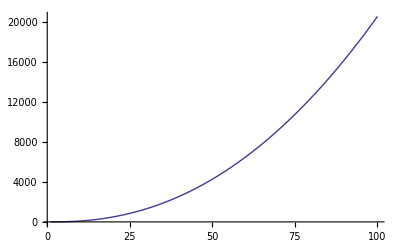

```mathematica
oldr=Exp[
Plot[myr,{r,1,100}]
```

```mathematica
fun1=Integrate[1/(r*Log[r]),r]
Solve[fun1==C,r]
```

Log[Log[r]]

{{r→ⅇ^(ⅇ^C)}}

1/2+ArcTan[(x-x0)/C]/π

1/2+ArcTan[1/5 (-80+x)]/π

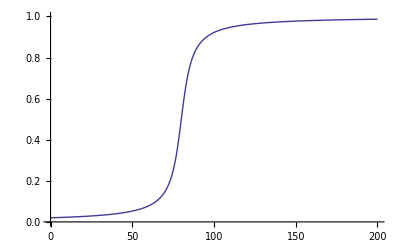

```mathematica
AT=(1/Pi)*ArcTan[(x-x0)/C]+1/2
ATplot=AT//.{x0->80,C->5}
Plot[ATplot,{x,0,200},PlotRange->{0,1}]
```

```mathematica
(* Setup new exp-exp grid *)
```

```mathematica
TS=512
i0=TS/2
(*ii1=TS/2*)
CC=5
a=92/100
(*iihor=4*)
rhor=1+Sqrt[1-a^2]
Rin=12/10
Rout=10^(10)
Rj=200  (* radius by which is *very* monopolar *)
Rj2=10^5
(*drhor=rhor/10*)
dr0=(rhor-Rin)/5
```

512

256

5

23/25

1+(4 √6)/25

6/5

10000000000

200

100000

1/5 (-1/5+(4 √6)/25)

```mathematica
(* try not choosing dr *)
```

```mathematica
(*
myAT=(1/Pi)*ArcTan[(ii-i0)/CC]+1/2
myAT=1
fun=AA+Exp[A*ii+Exp[B+D*ii]*myAT]
dfun=D[fun,ii]
dr0eq=(dr0==dfun//.{ii->0})
eq1=(fun==Rin)//.{ii->0}
eq2=(fun==Rout)//.{ii->TS}
eq3=(fun==Rj)//.{ii->TS/2}
(*sol=FindRoot[{dr0eq,eq1,eq2,eq3},{{AA,-.01},{A,0.02},{B,-.001},{D,.01}},MaxIterations->1000,WorkingPrecision->150]*)
sol=FindRoot[{dr0eq,eq1,eq2,eq3},{{AA,-1,0},{A,-.5,0.5},{B,-1,0},{D,0,.03}},Method->"Secant",MaxIterations->10000,WorkingPrecision->400]
*)
```

1/2+ArcTan[1/5 (-128+ii)]/π

1

1999999/10000000+ⅇ^(ⅇ^(B+D ii)+A ii)

ⅇ^(ⅇ^(B+D ii)+A ii) (A+D ⅇ^(B+D ii))

1/5 (-1/5+(4 √6)/25)==ⅇ^(ⅇ^B) (A+D ⅇ^B)

1999999/10000000+ⅇ^(ⅇ^B)==6/5

1999999/10000000+ⅇ^(256 A+ⅇ^(B+256 D))==10000000000

1999999/10000000+ⅇ^(128 A+ⅇ^(B+128 D))==200

$Aborted

```mathematica
(* NOW USING THIS ONE, NOT ANY OTHER VERSION *)
```

```mathematica
(* Try reforming f -- NOW USING THIS ONE, NOT ANY OTHER VERSION *)
```

```mathematica
myAT=(1/Pi)*ArcTan[(ii-i0)/CC]+1/2;
myAT=1;
AA=1999999/10000000;
AA=0.19999999999999
(*AA=0.15*)
N[AA]
fun=A*ii+Exp[B+D*ii]*myAT;
(*
dfun=D[fun,ii];
dr0eq=(dfun==dr0/(Rin-AA))//.{ii->0}
*)
eq1=(fun==Log[Rin-AA])//.{ii->0}
eq2=(fun==Log[Rout-AA])//.{ii->TS}
eq3=(fun==Log[Rj-AA])//.{ii->TS/2}
(*sol=FindRoot[{dr0eq,eq1,eq2,eq3},{{AA,-.01},{A,0.02},{B,-.001},{D,.01}},MaxIterations->10000,WorkingPrecision->1000]*)
sol=FindRoot[{eq1,eq2,eq3},{{A,0.02},{B,-.001},{D,.01}},MaxIterations->10000,WorkingPrecision->1000]
```

0.2

0.2

ⅇ^B==9.99201×10^-15

512 A+ⅇ^(B+512 D)==23.0259

256 A+ⅇ^(B+256 D)==5.29732

FindRoot::precw: The precision of the argument function ({ⅇ^B == 9.99201×10^-15, 512\ A + ⅇ^B + 512\ D == 23.0259, 256\ A + ⅇ^B + 256\ D == 5.29732}) is less than WorkingPrecision (1000.).

{A→0.02069264263193774599646938012644077432381382638892575503072508384500102158948642142303775218456746593380406748465124709643373591104146913603571940411942573235800366632000174684541017679323278745862328269979347187177932628585178268350660291588861202314097577232753016494276607639780240806932259035286300290543655277915245712731919683298460168883976903578655917598834489884796393093725933333920288921276772253239262910557111616308419961533434202087948497358443746644257877760424478332015415078989619264304724537648018207155406466282161481125391694022860944698894649134609752329244105231265245472957267923768871214927355153679065225324884290480819532296480561402213163989937243781760917767017489999266943651506273298664214713697048922396804617002305384068625423170122227701874624291281903779911216833882021841874741868663247676520346067029113650788899718978502176289498450918423338088327170177111632084756005927317015579011471857779674754856860430279481234908530624038246328226963046990079518170857067898,B→-32.23699089934684138505316369170136270756554072764068233609987091818795071373690402733694623282614010060688711284915911189641321842264173754844414833585460852267289160791999175833688252949379107843515153843498732411869928119361641568475369916408797660814311155482903892791214117917611650619312774730512497338193540522904587197353915870238203705114458140436877884491049911758338947008648872906912228453224854916898746314970385906588542646443359906641641985942346844042441522285751325732518316439428809437979607880753355398269156841574256127738977212186165478351643590985665767704182651995726138211431860971503744685097076854550142467195322224448841875612438203961076821710264841334510007246929955916302151452597183294106679340003194156515126974442039124232651505548280721826589724285365736425516429665775723502264498066079800145472479121529078083852723832646376053673729602145596399322911940888219110582072656629364718409733438050976557866368519638090024383529592573649293323819503229898562513151856227,D→0.06788515972842198406142175106130522268249109080231044837917269160274320843493985512127506110553762555297246065839765573576693523091559313627693265184154429434257074745787133849481830482095218520127565470599497789095598279979964374961374668961780862941539144792047721871397715043489318207472308232892318601281784569000822592212893187660015081105231985410183816684988215256961079654076637013786070681627468392256595432730962426846996935302847700227206910687083020718320478988266501733960895577527894150512248831420548561478432899585063955699568329147720303331247074786651116695486426484388292950509919795926010058553223857248163888149715286473802145846326956431872720189354037238006877653263380455589698243573565234565522384634746774093634694850736247771288947345967677661548836155677592475503782611212063084379221897679747312399344190134971645017360835255963838477818062480697738367648151027933766163354434426822978304112488215610645844494638562326354656086651219791460737500674770831814047241139063703}

```mathematica
(* AA,G1,G2,G3,ii2,CC2*)
Clear[AA,BB,G1,G2,G3,ii2,CC2]
myAT=(1/Pi)*ArcTan[(ii-i0)/CC]+1/2;
myAT=1;
fun=G1+G2*ii^(G3)+Exp[(ii+ii2)*CC2]*myAT;
eq1=(fun==Log[Rin+AA+BB*ii])//.{ii->0}
eq2=(fun==Log[Rin+dr0+AA+BB*ii])//.{ii->1}
eq2b=(fun==Log[Rin+2.1*dr0+AA+BB*ii])//.{ii->2}
eq3=(fun==Log[Rj+AA+BB*ii])//.{ii->TS/2}
eq4=(fun==Log[Rj2+AA+BB*ii])//.{ii->3*TS/4}
eq5=(fun==Log[Rj2*10+AA+BB*ii])//.{ii->5*TS/6}
eq6=(fun==Log[Rout+AA+BB*ii])//.{ii->TS}
sol=FindRoot[{eq1,eq2,eq2b,eq3,eq4,eq5,eq6},{{AA,0.1},{BB,0.1},{G1,1},{G2,0.1},{G3,.1},{ii2,1},{CC2,.1}},MaxIterations->10000,WorkingPrecision->1000]
```

ⅇ^(CC2 ii2)+G1+0^G3 G2==Log[6/5+AA]

ⅇ^(CC2 (1+ii2))+G1+G2==Log[6/5+1/5 (-1/5+(4 √6)/25)+AA+BB]

ⅇ^(CC2 (2+ii2))+G1+2^G3 G2==Log[1.28061+AA+2 BB]

ⅇ^(CC2 (256+ii2))+G1+256^G3 G2==Log[200+AA+256 BB]

ⅇ^(CC2 (384+ii2))+G1+384^G3 G2==Log[100000+AA+384 BB]

ⅇ^(CC2 (1280/3+ii2))+G1+(1280/3)^G3 G2==Log[1000000+AA+(1280 BB)/3]

ⅇ^(CC2 (512+ii2))+G1+512^G3 G2==Log[10000000000+AA+512 BB]

FindRoot::precw: The precision of the argument function ({ⅇ^CC2\ ii2 + G1 + 0^G3\ G2 == Log[6/5 + AA], ⅇ^CC2\ (1 + ii2) + G1 + G2 == Log[6/5 + 1/5\ (-1/5 + 4/25\ Power[« 2 »]) + AA + BB], « 3 », ⅇ^CC2\ (1280/3 + ii2) + G1 + (1280/3)^G3\ G2 == Log[1000000 + AA + 1280\ BB/3], ⅇ^CC2\ (512 + ii2) + G1 + 512^G3\ G2 == Log[10000000000 + AA + 512\ BB]}) is less than WorkingPrecision (1000.).

∞::indet: Indeterminate expression 0\ (-∞) encountered.

FindRoot::njnum: The Jacobian is not a matrix of numbers at {AA, BB, G1, G2, G3, ii2, CC2} = {0.1, 0.1, 1., 0.1, 0.1, 1., 0.1}.

{AA→0.1,BB→0.1,G1→1.,G2→0.1,G3→0.1,ii2→1.,CC2→0.1}

```mathematica
(* Try again since above transitions too late *)
```

```mathematica
(*Clear[CC1,ii1,CC2,ii2,AA]
myAT=(1/Pi)*ArcTan[(ii-i0)/CC]+1/2;
myAT=1;
fun=(ii-ii2)*CC2+Exp[(ii-ii1)*CC1]*myAT;
eq1=(fun==Log[Rin-AA])//.{ii->0}
eq5=(fun==Log[Rin+dr0-AA])//.{ii->1}
eq2=(fun==Log[Rout-AA])//.{ii->TS}
eq3=(fun==Log[Rj-AA])//.{ii->TS/2}
eq4=(fun==Log[Rj2-AA])//.{ii->3*TS/4}
(*sol=FindRoot[{eq1a,eq1,eq2,eq3,eq4},{{AA,0},{ii2,TS},{CC2,1},{ii1,TS},{CC1,1}},MaxIterations->10000,WorkingPrecision->1000]*)
(*sol=FindRoot[{eq5,eq1,eq2,eq3,eq4},{{AA,-10,1},{ii2,-TS,TS},{CC2,0.0001,1.0},{ii1,-TS,TS},{CC1,0.0001,1.0}},Method->"Secant",MaxIterations->10000,WorkingPrecision->1000]*)
sol=FindRoot[{eq5,eq1,eq2,eq3,eq4},{{AA,-3},{ii2,-10},{CC2,.01},{ii1,TS},{CC1,.01}},MaxIterations->10000,WorkingPrecision->1000]
*)
```

```mathematica
(* separate tests work *)
(*
CC1=0
ii1=0
Clear[ii2,CC2]
(*sol=FindRoot[{eq1a,eq1,eq2},{{AA,-100,100},{ii2,0,TS},{CC2,0.0001,100.0}},Method->"Secant",MaxIterations->10000,WorkingPrecision->1000]*)
sol=FindRoot[{eq1a,eq1,eq2},{{AA,1.0},{ii2,TS/2},{CC2,1.0}},MaxIterations->10000,WorkingPrecision->1000]
*)
```

```mathematica
(* separate tests work *)
(*
CC2=0
ii2=0
Clear[ii1,CC1]
(*sol=FindRoot[{eq1a,eq1,eq2},{{AA,-100,100},{ii2,0,TS},{CC2,0.0001,100.0}},Method->"Secant",MaxIterations->10000,WorkingPrecision->1000]*)
sol=FindRoot[{eq1a,eq1,eq2},{{AA,1.0},{ii1,TS/2},{CC1,0.001}},MaxIterations->10000,WorkingPrecision->1000]
*)
```

```mathematica
(*CForm[sol]*)
```

1.1901327454784616632323874471675019391713467677013536090179388869489786881455881147417793275623699258162094018965982766672475880815742059995100480740294366250425113722347663394734641669355560576678543065013581668236362193222440223886683286633059619094489406131271287691135582558690838869467691078939692431040003395164088605139654343180978722535625012670440028813146909661294285761958512573617711054979628292788809476658198441025524635012007906900956154733795031066591962648257696055151000629442737904779318399625550453058911853022740817283124237579539791152886322770755314087863204960878720159846516568583376799163587984941098183355515609975917217620326772371130488957856806007691180852257618049922753188897027094723973983599168908473802146629833867776010506010399489930058680771017133968848947951746172615878373842294938084517270913332398059664017058944705809565437822613293874935345128194691955026361452814631102346144609944563825687094389938004739905305076538665150044088498524446453351214940146

0.009867254521538336767612552832498060828653232298646390982061113051021311854411885258220672437630074183790598103401723332752411918425794000489951925970563374957488627765233660526535833064443942332145693498641833176363780677755977611331671336694038090551059386872871230886441744130916113053230892106030756895999660483591139486034565681902127746437498732955997118685309033870571423804148742638228894502037170721119052334180155897447536498799209309904384526620496893340803735174230394484899937055726209522068160037444954694108814697725918271687576242046020884711367722924468591213679503912127984015348343141662320083641201505890181664448439002408278237967322762886951104214319399230881914774238195007724681110297290527602601640083109152619785337016613222398949398960051006994131922898286603115105204825382738412162615770506191548272908666760194033598294105529419043456217738670612506465487180530804497363854718536889765385539005543617431290561006199526009469492346133484995591150147555354664878505985398

6.9652369882345876879105852843165212300007601010406621199535736669929521410758831386650106836408630110088101728104097410901446559535363224497824273139607598612764521622994671248893252715061395874646108519580300907889759765030766407391462030594665886156678279520368660328526707358735484034668032735206435891262323252293006783583699737061143149680159367324138738706630798693432942993419540681464160553392304193044022061566988965600063832938466536466309527346986849128532626426843808900130202474719377899725213326068514729279307974825538563681800690670905686732804059172309753027084374072934822956600531352888967434727079034176057951925299284076895641591711842711705898573301770675348173610570053849952368410422997136932147116140261724527501979033250159669748374320352416949171730954133650683531316853384227208443626018590629298564083398811633656747266984932238669789928615012565041784441425858834083304969775697830810977099700630746516390962791045302644790964609629960554106882383076847858120792824×10^55

5267.9149213488316343680216836628863118534642241748502348618227010805509143062866338450282981617001443569859459713130395293494951497641220578298113719809262168828201476397480822162459013805966826894344191227177485162604490370909475119847295377209133602714857474222687217037737060003780147268835300729065574445029273764372014693762525073658789337586820887489654950524417413902346831655533780531475877192972216870121474320269615529492258112364174328270087562540090091908107318293131377320113842409252734925527751943950164958503913914637165470539282843445305597571884066542207985689406289028321976524940121632180937253403705425623603403845576081319109398711621334461586465532407541583551508913815878715319945051434474244091614677683355591304682254158716617298726694240479115612126714725667864006646534741435475171135600074641929922476380690867365231245009156545994062652741241695713754486166449241830616261134326732699757143198615898345292052282770031050256155777752973048137707032160640729670750000949

Compare dr

0.0106961759041512157073271271990999067816175616808863845911013180075692769849007379348955359187900403334587584357282713721049843917725860832418296434720146165930057531282251346597760439045583457136276998337406254491297725579071649557490696399232797143131619917289604922759988466053330960618793365949535215012407263519743205045860398727200191122348762990090092122961427651754426297384073019432322047970816222715968190771547299833411547127585389762676077135945497766113316711429895878907118609570778558290743787004134682715236537632946377316534270442888584213045266389502206115042716008314141183775217943714432883312054924602596661312984904077905332152602705381308748302857441181608677473003451645163683405742075440004034790845735261397306016295038308994812830200231227625211874943986182357430680930591098816635150272684684491871077232178748071309088961294315573662615640629479090811702552829015112789330263322319873656289890207387110875585242590638581814113005871275601132941275348471248736697613874466

0.0383837

dr/r

0.00898738056304055280407591301275775919206566192124617557327318150085065546506545530152194234649802796004619032576666442036616316877898136012811979803083661339735948522428596493013132167766548458892615295989689397622308364593758470573891910581994123810829498422094269606361703424228576065840889118774970113495993899341369662719625089317208282595069782045566500155870353394024445742878518383092060910244977129254986017694416232417352457813665971291455897355860520777870389578059371526294670028265575580113384474850250116774765941552905307518917147631623506842779336397526368691829462063845916996349070195535855795744808322007109719352493549176474700604827494020710569937335739479492958856187314274317499377402987251920012367411801955795128536279855807414219595811230896629125547436173575686310393652601299754297411911117989647445250404444722078516621994203070288957918515189243821168870177838510401704625822123101670521796401598093291377965383994748291146772377154848482097319656481055327954463714236754

-Graphics-

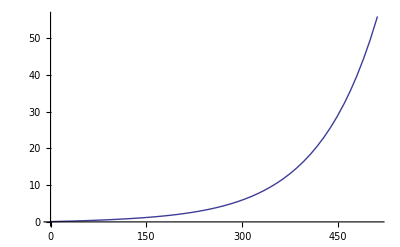

```mathematica
funplot=(Exp[fun]+AA)//.sol;
funplot//.{ii->0}
Rin-funplot//.{ii->0}
funplot//.{ii->TS}
funplot//.{ii->TS/2}
Print["Compare dr"];
finaldr0=D[funplot,ii]//.{ii->0}
(rhor-Rin)/5.0
Print["dr/r"];
finaldror=finaldr0/(funplot//.{ii->0})
Plot[funplot,{ii,0,TS}]
Plot[Log[10,funplot],{ii,0,TS}]
```

```mathematica
(* not working method *)
```

```mathematica
(*myAT=(1/Pi)*ArcTan[(ii-i0)/CC]+1/2
myAT=1
fun=AA+Exp[A*ii+Exp[B+D*ii]*myAT]
(*
dr0eq=N[drhor==D[fun,ii]//.{ii->iihor}]
eq1=N[(fun==rhor)//.{ii->iihor}]
*)
dfun=D[fun,ii]
dr0eq=N[dr0==dfun//.{ii->0},20]
eq1=N[(fun==Rin)//.{ii->0},20]
eq2=N[(fun==Rout)//.{ii->TS},20]
eq3=N[(fun==Rj)//.{ii->TS/2},20]
sol=FindRoot[{dr0eq,eq1,eq2,eq3},{{AA,-1.0},{A,0.01},{B,-1},{D,.01}},MaxIterations->100000]
(*sol=Module[{s=0,e=0},{FindRoot[{dr0eq,eq1,eq2,eq3},{{AA,-.1,.1},{A,-.1,.1},{B,-3,-1},{D,-.1,.1}},Method->"Secant",StepMonitor:>s++,EvaluationMonitor:>e++],"Steps"->s,"Evaluations"->e}]*)
*)
```

```mathematica
(* try simple case of pure exp-exp grid *)
```

ⅇ^(ⅇ^(B+D ii))

2.7182818284590452354^(2.7182818284590452354^B)==1.2

2.7182818284590452354^(2.7182818284590452354^(B+512. D))==1.×10^10

{B→-1.70198,D→0.00945039}

ⅇ^(ⅇ^(-1.70198+0.00945039 ii))

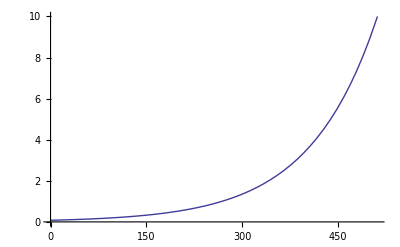

```mathematica
fun=AA+Exp[A*ii+Exp[B+D*ii]]//.{AA->0,A->0}
eq1=N[(fun==Rin)//.{ii->0},20]
eq2=N[(fun==Rout)//.{ii->TS},20]
sol=FindRoot[{eq1,eq2},{{B,-1.0},{D,.01}},MaxIterations->1000]
funplot=fun//.sol
Plot[Log[10,funplot],{ii,0,TS}]
```

```mathematica
(* Now try simple exp case *)
```

AAQ+ⅇ^(1+A ii)

2.7182818284590452354+AAQ==1.2

2.7182818284590452354^(1.+512. A)+AAQ==1.×10^10

{AAQ→-1.51828,A→0.0430192}

-1.51828+ⅇ^(1+0.0430192 ii)

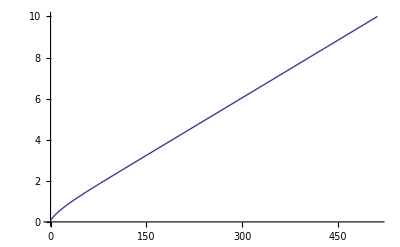

```mathematica
fun=AAQ+Exp[A*ii+Exp[B+D*ii]]//.{B->0,D->0}
eq1=N[(fun==Rin)//.{ii->0},20]
eq2=N[(fun==Rout)//.{ii->TS},20]
sol=FindRoot[{eq1,eq2},{{AAQ,0},{A,0}},MaxIterations->1000]
funplot=fun//.sol
Plot[Log[10,funplot],{ii,0,TS}]
```

```mathematica
(* my pick and choose to probe B and D *)
```

ⅇ^(ⅇ^(-1.5+0.013 ii))

1.24998

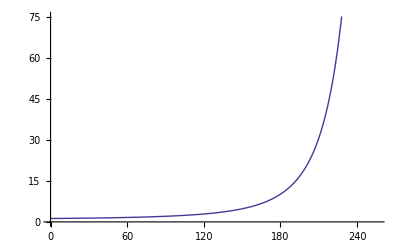

```mathematica
(*funtest=fun//.{D->.0064,B->-1.5}*)
funtest=fun//.{D->.013,B->-1.5}
funtest//.{ii->0.}
Plot[funtest,{ii,0,TS}]
```

```mathematica
(* CHECK *)
```

```mathematica
funplot//.{ii->0}
Rin-funplot//.{ii->0}
rhor-funplot//.{ii->iihor}
funplot//.{ii->TS}
funplot//.{ii->TS/2}
D[funplot,ii]//.{ii->0}
```

1.32757

-0.127568

-0.0135772

102.041

64.5849

0.0188505

```mathematica
(* Work out polar axis warp *)
```

128

Log[Tan[h/2]]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2 ArcTan[ⅇ^(j YY+ZZ)]

2 ArcTan[ⅇ^ZZ]==0

2 ArcTan[ⅇ^(64 YY+ZZ)]==π/2

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{YY→1.,ZZ→-9.11661×10^-41}

2 ArcTan[ⅇ^(-9.11661×10^-41+1. j)]

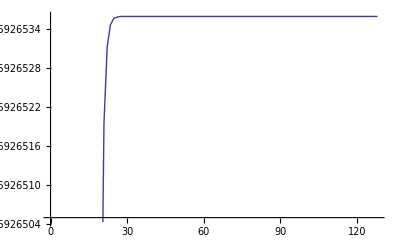

```mathematica
N2=128
funwarp=Integrate[1/Sin[h],h]
myh=Solve[funwarp==YY*j+ZZ,h][[1,1,2]]
eq1=(myh==0)//.{j->0}
eq2=(myh==Pi/2)//.{j->N2/2}
mysol=FindRoot[{eq1,eq2},{YY,1},{ZZ,0}]
finalmyh=myh//.mysol
Plot[finalmyh,{j,0,N2}]
```

```mathematica
(* Check *)
```

```mathematica
finalmyh//.{j->0}
finalmyh//.{j->N2/2}
finalmyh//.{j->N2}
```

1.5708

3.14159

3.14159

(8.24383×10^14 ⅇ^(1.05011 j) Csc[2 ArcTan[2.54763×10^-15 ⅇ^(1.05011 j)]])/(1.54073×10^29+ⅇ^(2.10023 j))

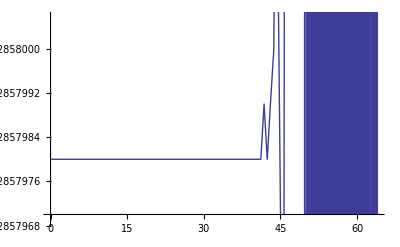

```mathematica
crap=FullSimplify[D[finalmyh,j]/Sin[finalmyh]]
Plot[crap,{j,0,N2}]
```

```mathematica
(* try again *)
```

```mathematica
finaldror
N3=64
dphi=2*Pi/N3
nearpoledh=finaldror/dphi
```

0.0344549745461865380127315321611772017568319515939843015437995513556589168483394710914714672772528997505617371063624791716708590806982065406550880857849630364695920328544651112022523080169699905284918120036791909942920355019298104884787944052195823380869072051961650265308483747158622302777812712975898103468868976615324669327797578682652303079554321579417538097101951091565318744027852968638612293776722132589341128467803221687705230642629425796075256702526623091243447087921404274203133549845652254432189777621796563064390687206054686019998445823356490958173020314767294765651432244913108153325808402390462194739625755878368210781085635570198886328918674668463238445040730608003442202216744721785783005676740649504649830898224986580473230279395614276449167567427943147479024870420094275272684717326285208352329528573053045759226805662962615775946740485717965310293504443415400388406356460792068867977820617330965834260469488068586782170430757970829203327132670222320142388353495932981493241764415674

64

π/32

0.350955488840385329895281641891911569963553816372922090258947752039716877469342673147201801688203403236620525636977225075165838027503028181497647301118499596622796846595120538580786513014551847975812585264217887091844974135906677075741724516728688063544354520437323973388748669964771402869603244926269561222953641278595673211197722118545242078474222742901597048429209755006912432656298241373673626062531631839628094500595265044578155998009294043830686102140843711144986911217067506777229765511078129155250678955771704350352255218226326337017163730322826271129899320036528010429313953414776847976058578861342780290251282196009523487034935482522892269836004419591982648451263481729447085028503237421885452965057895727574235778437798143957240766591958713842187790929143970471988443243970547198807208145847583831943529715665464222560355160024829342925986863065358815486803221297953849902036514811868385348879615042219117540276245959505720921168808278095054892472359600843394727188565194361453114306863436

```mathematica
Pi/128.0
```

0.0245437

```mathematica
N2=128
x2=jj/N2
j0=1
CCj=50
func=(1+ArcTan[(jj-j0)/CCj]/ArcTan[j0/CCj])/2
myAT=If[jj<j0,0,1]
h1=-8
h2=0.3
h=h2*myAT+h1*(1-myAT)
godtheta=Pi*x2+ (1-h)/2*Sin[2*Pi*x2]
(*crap1=godtheta//.{j->1}
Plot[crap1,{h,-1,10}]
Solve[crap1==Pi/N2*10.,h]
*)
```

128

jj/128

1

50

1/2 (1+ArcTan[1/50 (-1+jj)]/ArcTan[1/50])

If[jj<1,0,1]

-8

0.3

-8 (1-If[jj<1,0,1])+0.3 If[jj<1,0,1]

(jj π)/128+1/2 (1+8 (1-If[jj<1,0,1])-0.3 If[jj<1,0,1]) Sin[(jj π)/64]

```mathematica
godtheta//.{jj->1}
```

0.0417174

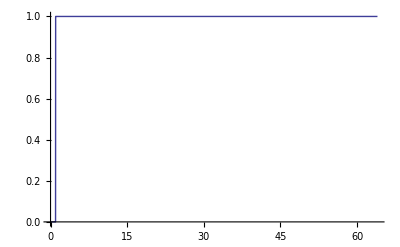

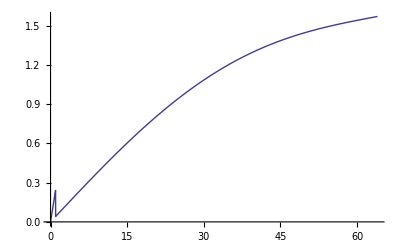

```mathematica
Plot[myAT,{jj,0,N2/2}]
Plot[godtheta,{jj,0,N2/2}]
```

```mathematica
(* another attempt *)
```

```mathematica
N2=128
x2=jj/N2
CCj=N2/50
j0=N2/4
func=(1+ArcTan[(jj-j0)/CCj]/ArcTan[j0/CCj])/2
myAT=If[jj<N2/2,func,1]
h1=.2
h2=8
h=h2*myAT+h1*(1-myAT)
Clear[h]
newtheta=(Pi/2)*(1+ArcTan[h*(x2-1/2)]/ArcTan[h/2])
Plot[newtheta,{jj,0,N2/2}]
```

128

jj/128

64/25

32

1/2 (1+ArcTan[25/64 (-32+jj)]/ArcTan[25/2])

If[jj<64,func,1]

0.2

8

0.2 (1-If[jj<64,func,1])+8 If[jj<64,func,1]

1/2 π (1+ArcTan[h (-1/2+jj/128)]/ArcTan[h/2])

Plot::exclul: {Re[h\ (-1/2 + jj/128)] - 0} must be a list of equalities or real-valued functions.

-Graphics-

π/2-(π ArcTan[(63 h)/128])/(2 ArcTan[h/2])

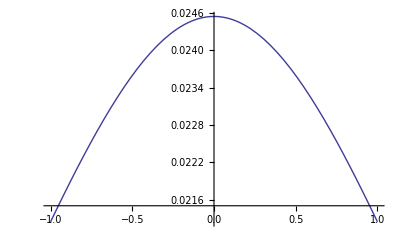

```mathematica
crap=Normal[Series[newtheta,{jj,1,1}]]//.{jj->1}
Plot[crap,{h,-1,1}]
```

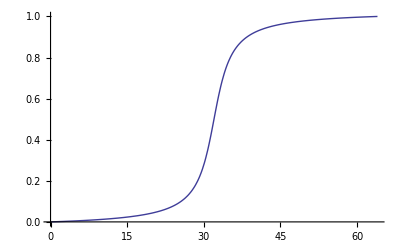

```mathematica
Plot[myAT,{jj,0,N2/2}]
```